```mathematica
f[s_,R_]:= s^2/R^2;
g[s_,uT_]:= 1/(√(1-(uT/s)^4));
x[sm_,uT_,R_,s0_]:=NIntegrate[(f[s,R]/g[s,uT] (√(f[s,R]^2-f[s0,R]^2))/f[s0,R]^2)^-1,{s,Max[s0,uT],sm}];
x2[sm_,uT_,R_,c_]:=NIntegrate[(f[s,R]/g[s,uT] (√(f[s,R]^2-c^2))/c^2)^-1,{s,Max[s0,uT],sm}];
```

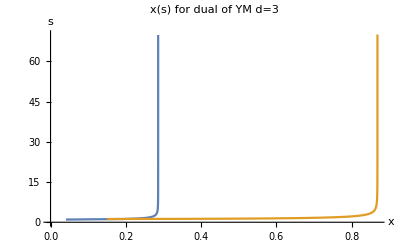

0.0381707

0.000299544

```mathematica
ListPlot[{Table[{x[s,1,1,0.8],s},{ s,1.006,70,0.2}],Table[{x[s,1,1,1.2],s},{ s,1.21,70,0.05}]},PlotLabel->"x(s) for dual of YM d=3",AxesLabel->{"x","s"},Joined->True]
x[Infinity,1,1,0.5]
x[Infinity,5,1,0.5]
```

```mathematica
x[1.01,1,1,0.5]
```

0.00639364